```mathematica
Get["~/maths/ibmer/papers/mdgp/intro_dg/DGPSystem.m"]
```

```mathematica
G=Graph[{1<->2,2<->3,3<->1,1<->4,4<->2},VertexLabels->"Name",EdgeWeight->{1,2,2,1,1}]
K=2
```

-Graphics-

2

```mathematica
myVars=Array[x,{Length[VertexList[G]],K}]
S=DGPSystemSquaredVars[G,K,myVars]
```

{{x[1,1],x[1,2]},{x[2,1],x[2,2]},{x[3,1],x[3,2]},{x[4,1],x[4,2]}}

{(x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2==1,(x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2==4,(-x[1,1]+x[3,1])^2+(-x[1,2]+x[3,2])^2==4,(x[1,1]-x[4,1])^2+(x[1,2]-x[4,2])^2==1,(-x[2,1]+x[4,1])^2+(-x[2,2]+x[4,2])^2==1}

```mathematica
IncongruentSolutions={x[1,1]->0,x[1,2]->0,x[2,1]->1}
SI=S/.IncongruentSolutions
```

{x[1,1]→0,x[1,2]→0,x[2,1]→1}

{1+x[2,2]^2==1,(1-x[3,1])^2+(x[2,2]-x[3,2])^2==4,x[3,1]^2+x[3,2]^2==4,x[4,1]^2+x[4,2]^2==1,(-1+x[4,1])^2+(-x[2,2]+x[4,2])^2==1}

```mathematica
sol=Solve[Apply[And,SI],Flatten[myVars],Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[2,2]→0,x[3,1]→1/2,x[3,2]→-(√15)/2,x[4,1]→1/2,x[4,2]→-(√3)/2},{x[2,2]→0,x[3,1]→1/2,x[3,2]→-(√15)/2,x[4,1]→1/2,x[4,2]→(√3)/2},{x[2,2]→0,x[3,1]→1/2,x[3,2]→(√15)/2,x[4,1]→1/2,x[4,2]→-(√3)/2},{x[2,2]→0,x[3,1]→1/2,x[3,2]→(√15)/2,x[4,1]→1/2,x[4,2]→(√3)/2}}

```mathematica
sol2=myVars/.IncongruentSolutions/.sol
```

{{{0,0},{1,0},{1/2,-(√15)/2},{1/2,-(√3)/2}},{{0,0},{1,0},{1/2,-(√15)/2},{1/2,(√3)/2}},{{0,0},{1,0},{1/2,(√15)/2},{1/2,-(√3)/2}},{{0,0},{1,0},{1/2,(√15)/2},{1/2,(√3)/2}}}

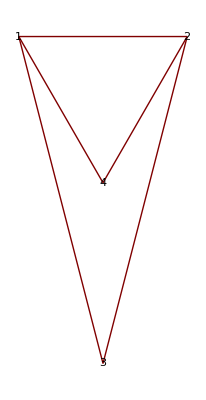
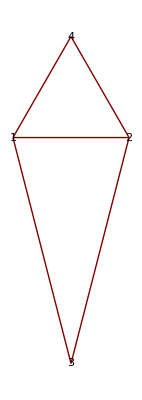
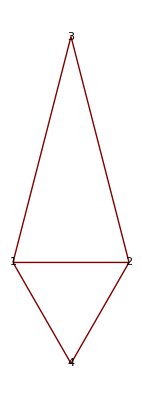
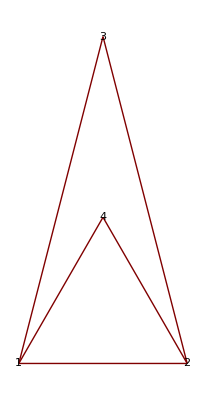

```mathematica
Map[GraphPlot[G,VertexLabeling->True,VertexCoordinateRules->#]&,sol2]
```

```mathematica
WeightedGraphQ[G]
```

True

```mathematica
x={{0,0}, {0,1}, {1,0}}
```

{{0,0},{0,1},{1,0}}

```mathematica
MyVars = Array[y, 2]
```

{y[1],y[2]}

```mathematica
d={Sqrt[2], 1, 1}
```

{√2,1,1}

```mathematica
MySystem = Map[(2 (x[[#]]-x[[3]]).MyVars == Norm[x[[#]]]^2-Norm[x[[3]]]^2 -d[[#]]^2+d[[3]]^2)&, Range[2]]
```

{-2 y[1]==-1.9881,2 (-y[1]+y[2])==0}

```mathematica
sol = Solve[{-2 y[1]==-2,2 (-y[1]+y[2])==0},{y[1],y[2]}]
```

{{y[1]→1,y[2]→1}}

```mathematica
Flatten[MyVars /. sol]
```

{1,1}

```mathematica
sol = LinearSolve[Apply[And,MySystem], MyVars]
```

LinearSolve[-2 y[1]==-1.9881&&2 (-y[1]+y[2])==0,{y[1],y[2]}]

```mathematica
ReplaceAll[MyVars, sol]
```

{{1,1}}

ReplaceAll::argr: ReplaceAll called with 1 argument; 2 arguments are expected.

Reduce::naqs: {1, 1} is not a quantified system of equations and inequalities.

```mathematica
MyVars
```

{y[1],y[2]}

```mathematica
sol
```

{{y[1]→1,y[2]→1}}

```mathematica
NextVertexUnique[x_List?MatrixQ,d_List,K_Integer?Positive]:=Block[{MyVars,MySystem},MyVars=Array[y,K-1];
MySystem=Map[(2 (x[[#]]-x[[K]]).MyVars==Norm[x[[#]]]^2-Norm[x[[K]]]^2-d[[#]]^2+d[[K]]^2)&,Range[K-1]];
sol=Solve[Apply[And,MySystem],MyVars];
Return[Flatten[MyVars/.sol]]]
```

```mathematica
NextVertexUnique[x, d, 3]
```

{0.99405,0.99405}

```mathematica
MyVars = Array[y, 3]
```

{y[1],y[2],y[3]}

```mathematica
MyMatrix=Map[(2 (x[[#]]-x[[K]]))&,Range[K-1]]
```

{{0,-2,0},{2,-2,0}}

```mathematica
MyRHS=Map[(Norm[x[[#]]]^2-Norm[x[[K]]]^2-d[[#]]^2+d[[K]]^2)&,Range[K-1]]
```

{-1,0}

```mathematica
K=3
```

3

```mathematica
d={1,1,1}
```

{1,1,1}

```mathematica
MyMatrix.MyVars == MyRHS
```

{-2 y[2],2 y[1]-2 y[2]}=={-1,0}

```mathematica
x={{0,0,0}, {1,0,0}, {0,1,0}}
```

{{0,0,0},{1,0,0},{0,1,0}}

```mathematica
x0 = LinearSolve[MyMatrix, MyRHS]
```

{1/2,1/2,0}

```mathematica
v = Flatten[NullSpace[MyMatrix]]
```

{0,0,1}

```mathematica
t =.
```

```mathematica
x0 + t v
```

{1/2,1/2,t}

```mathematica
ns = NullSpace[MyMatrix]
```

{{0,0,1}}

```mathematica
nsd = Length[NullSpace[MyMatrix]]
```

1

```mathematica
tau = Array[t, nsd]
```

{t[1]}

```mathematica
x0+Flatten[tau ns]
```

{1/2,1/2,t[1]}

```mathematica
phi = {t[1], t[2]}
```

{t[1],t[2]}

```mathematica
psi = {{0,0,1}, {0,1,1}}
```

{{0,0,1},{0,1,1}}

```mathematica
x0 + phi.psi
```

{1/2,1/2+t[2],t[1]+t[2]}

```mathematica
x0 + tau.ns
```

{1/2,1/2,t[1]}

```mathematica
Solve[MyMatrix.MyVars == MyRHS && (EuclideanDistance[MyVars,x[[1]]])^2==(WeightedAdjacencyMatrix[G][[1,4]])^2, MyVars]
```

{{y[1]→1/2,y[2]→1/2,y[3]→-1/(√2)},{y[1]→1/2,y[2]→1/2,y[3]→1/(√2)}}

```mathematica
NextVertexPair[x_List?MatrixQ,d_List,K_Integer?Positive]:=Block[{MyVars,MyMatrix,MyRHS, y, sol},MyVars=Array[y,K];
MyMatrix=Map[(2 (x[[#]]-x[[K]]))&,Range[K-1]];
MyRHS=Map[(Norm[x[[#]]]^2-Norm[x[[K]]]^2-d[[#]]^2+d[[K]]^2)&,Range[K-1]];
MySystem={MyMatrix.MyVars==MyRHS,Sum[(MyVars[[k]]-x[[1,k]])^2,{k,K}]==d[[1]]^2};
sol=Solve[Apply[And,MySystem],MyVars];
Return[MyVars/.sol]]
```

```mathematica
NextVertexPair[x, d, K]
```

{{1/2,1/2,-1/(√2)},{1/2,1/2,1/(√2)}}

```mathematica
Map[(z[#] = #)&, Range[3]]
```

{1,2,3}

```mathematica
z[2]
```

2

```mathematica
Map[(x[#]=x0[#])&,Range[K+1]];
```

Set::write: Tag List in {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}}[1] is Protected.

Set::write: Tag List in {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}}[2] is Protected.

Set::write: Tag List in {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}}[3] is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

```mathematica
For[i=0, i<2, i++, Print[i];Break[]]
```

0

```mathematica
If[1==1,Print[1], ]
```

1

```mathematica
x = {{0,0},{1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],-(1/Sqrt[2])},{-3/(4*Sqrt[2])-(3*Sqrt[5/2])/4,(7+3*Sqrt[5])/(4*Sqrt[2])}}
```

{{0,0},{1/(√2),1/(√2)},{1/(√2),-1/(√2)},{-3/(4 √2)-(3 √(5/2))/4,(7+3 √5)/(4 √2)}}

```mathematica
Map[N, x, {2}]
```

{{0.,0.},{0.707107,0.707107},{0.707107,-0.707107},{-0.707107,-0.707107},{-0.707107,0.707107}}

```mathematica
x ={{0,0},{1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],-(1/Sqrt[2])},{-(1/Sqrt[2]),-(1/Sqrt[2])},{-(1/Sqrt[2]),1/Sqrt[2]}}
```

{{0,0},{1/(√2),1/(√2)},{1/(√2),-1/(√2)},{-1/(√2),-1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
K5=CompleteGraph[5,VertexLabels->"Name",EdgeWeight->{1,1,1,1,Sqrt[2],2,Sqrt[2],Sqrt[2],2,Sqrt[2]}]
```

-Graphics-

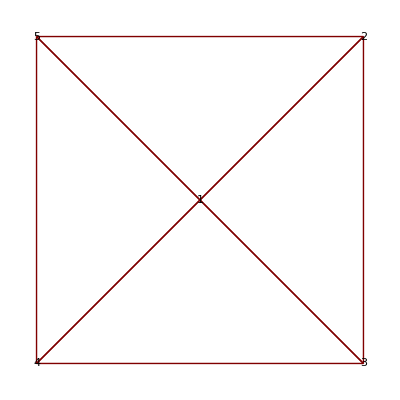

```mathematica
GraphPlot[K5, VertexLabeling-> True, VertexCoordinateRules ->x]
```